Model of the class problem.

Input: m - mass, R - radius of the cylinder, L - length of the cylinder, Omega - angular velocity around y-axis, theta0 - initial theta angle, damping - damping coefficient (it is zero in class problem, but its required to see “real-like” animation), Iyy and Jxx - moments of inertia).
Output: graph - represents theta with time, animation of the cylinder.
Modes: to see instability, put theta0=0.001  or  theta0=Pi/2-0.001 (and see that for Iyy>Jxx there is stable around Pi/2, and unstable around 0). For L=Sqrt[3]*R there is no rotation relative to the frame. Introduce damping (damping=0.02)  to see, that cylinder goes to the stable position with time.

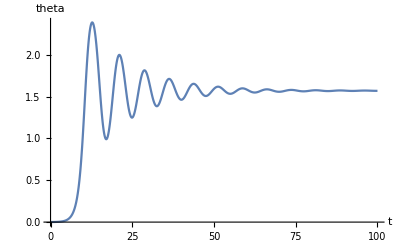

```mathematica
m=2;
R=0.2;
L=R*Sqrt[3]+0.5;
Omega=1;
theta0=0.001;
damping=0.02;
Iyy=m*R^2/2;
Jxx=m*R^2/4+m*L^2/12;

S=NDSolve[{Jxx*theta''[t]+damping*theta'[t]+(Iyy-Jxx)* Omega^2*Sin[theta[t]]*Cos[theta[t]]==0,theta[0]==theta0, theta'[0]==0},theta,{t,0,100},MaxStepSize->0.001];
th[t_]= theta[t]/.S;
y1[t_]=L/2*Cos[th[t]];
y2[t_]=-L/2*Cos[th[t]];
x1[t_]=L/2*Sin[th[t]]*Cos[Omega*t];
x2[t_]=-L/2*Sin[th[t]]*Cos[Omega*t];
z1[t_]=L/2*Sin[th[t]]*Sin[Omega*t];
z2[t_]=-L/2*Sin[th[t]]*Sin[Omega*t];
L2=1.25*(L+R);
Om0=Pi/2;
Plot[Evaluate[theta[t]/.S],{t,0,100},PlotRange->All,AxesLabel->{t, theta}]
a=Animate[Graphics3D[{Cylinder[{{x1[t].{1},y1[t].{1},z1[t].{1}},{x2[t].{1},y2[t].{1},z2[t].{1}}},R],Line[{{L2*Cos[Omega*t+Om0],-L2,L2*Sin[Omega*t+Om0]},{-L2*Cos[Omega*t+Om0],-L2,-L2*Sin[Omega*t+Om0]}}],Line[{{L2*Cos[Omega*t+Om0],L2,L2*Sin[Omega*t+Om0]},{-L2*Cos[Omega*t+Om0],L2,-L2*Sin[Omega*t+Om0]}}],Line[{{L2*Cos[Omega*t+Om0],-L2,L2*Sin[Omega*t+Om0]},{L2*Cos[Omega*t+Om0],L2,L2*Sin[Omega*t+Om0]}}],Line[{{-L2*Cos[Omega*t+Om0],L2,-L2*Sin[Omega*t+Om0]},{-L2*Cos[Omega*t+Om0],-L2,-L2*Sin[Omega*t+Om0]}}],
Line[{{-L2*Cos[Omega*t+Om0],0,-L2*Sin[Omega*t+Om0]},{L2*Cos[Omega*t+Om0],0,L2*Sin[Omega*t+Om0]}}]},PlotRange->{{-1.2*L2,1.2*L2},{-1.2*L2,1.2*L2},{-1.2*L2,1.2*L2}}],{t,0,100}, AnimationRate->5]
```